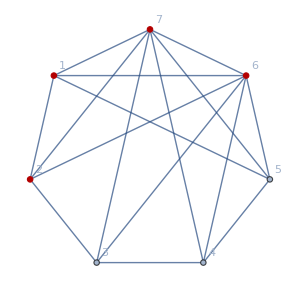
```mathematica
g2=-Graphics-;
```

```mathematica
GroupBy[Sort[Map[{SymbolLevel[#],#}&, FindFullFormula[g2]]],First]
```

<|5→{{5,v13x24x5x6x7},{5,v13x25x4x6x7},{5,v14x25x3x6x7},{5,v14x2x35x6x7},{5,v1x24x35x6x7}},6→{{6,v13x2x4x5x6x7},{6,v14x2x3x5x6x7},{6,v1x24x3x5x6x7},{6,v1x25x3x4x6x7},{6,v1x2x35x4x6x7}},7→{{7,v1x2x3x4x5x6x7}}|>

```mathematica
ChromaticPolynomial[g2,x]//Factor
```

(-4+x) (-3+x) (-2+x) (-1+x) x (10-6 x+x^2)